# Proyecto Mecanismos

## Datos

```mathematica
(*Planeteamos todas las constantes*)

(*-----Largo de los brazos del mecanismo-----*)

d1=0.20;

(*-----Largo de barra entre eslabones-----*)

d2=0.03;

(*-----Angúlo entre barras -----*)
β=120*Degree;
```

## Ecuaciones Cinemáticas

```mathematica
Clear[θ2,θ3,θ4];
Clear[ω2,ω3,ω4];
Clear[α2,α3,α4];
```

### Ecuaciones de Posición

```mathematica
u2={Cos[θ2],Sin[θ2],0};
u3={Cos[θ3],Sin[θ3],0};
u2p={Cos[θ2+β],Sin[θ2+β],0};
u3p={Cos[θ3+β],Sin[θ3+β],0};
u2bp={Cos[θ2+(2*β)],Sin[θ2+(2*β)],0};
u3bp={Cos[θ3+(2*β)],Sin[θ3+(2*β)],0};
u4={Cos[θ4],Sin[θ4],0};

R1={-d2,0,0};(*Distancia DAB*)
R2= d1*u2;(*Distancia DAD*)
R3= d1*u3;(*Distancia DBC*)
R4=d2*u4;(*Distancia DDC*)
R5={-d2,0,0};(*Distancia DEF*)
R6={-d2,0,0};(*Distancia DGH*)
R2p=d1*u2p;(*Distancia DAE*)
R3p=d1*u3p;(*Distancia DBF*)
R2bp=d1*u2bp;(*Distancia DAG*)
R3bp=d1*u3bp;(*Distancia DBH*)

(*-----Lazos Vectoriales Posición-----*)

pos1=R3+R4-R2-R1;
```

### Ecuaciones de Velocidad

```mathematica
omega2={0,0,ω2};
omega3={0,0,ω3};
omega4={0,0,ω4};

V1={0,0,0};
V2=omega2×R2;
V3=omega3×R3;
V4=omega4×R4;
V5={0,0,0};
V6={0,0,0};
V2p=omega2×R2p;
V3p=omega3×R3p;
V2bp=omega2×R2bp;
V3bp=omega3×R3bp;

(*-----Lazos Vectoriales Velocidad-----*)

vel1=V3+V4-V2-V1;
```

### Ecuaciones de Aceleración

```mathematica
alfa2={0,0,α2};
alfa3={0,0,α3};
alfa4={0,0,α4};

A1={0,0,0};
A2=alfa2×R2-ω2^2*R2;
A3=alfa3×R3-ω3^2*R3;
A4=alfa4×R4-ω4^2*R4;(*Suponiendo caso dos*)
A5={0,0,0};
A6={0,0,0};
A2p=alfa2×R2p-ω2^2*R2p;
A3p=alfa3×R3p-ω3^2*R3p;
A2bp=alfa2×R2bp-ω2^2*R2bp;
A3bp=alfa3×R3bp-ω3^2*R3bp;

(*Lazos Vectoriales Aceleración*)

acel1=A3+A4-A2-A1;
```

## Solución Posición

### Solución Inicial

```mathematica
Clear[θ2,θ3,θ4];
Clear[ω2,ω3,ω4];
Clear[α2,α3,α4];
```

```mathematica
θ3=1*Degree;(*Inicial*)

SolInicial=FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0},
{{θ2,1*Degree},
{θ4,90*Degree}},MaxIterations->15]
```

{θ2→0.0174533,θ4→3.14159}

```mathematica
{θ2->0.01745329251994633,θ4->3.141592653589773}
```

{θ2→0.0174533,θ4→3.14159}

### Solución Total

```mathematica
Clear[θ2,θ3,θ4];
Clear[ω2,ω3,ω4];
Clear[α2,α3,α4];
```

```mathematica
θ2i=(θ2/.SolInicial);
θ4i=(θ4/.SolInicial);

For[i=1,i≤360,i+=1,

θ3=i*Degree;

SolPos[i]=FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0},
{{θ2,θ2i},
{θ4,θ4i}},MaxIterations->50];

θ2i=θ2/.SolPos[i];
θ4i=θ4/.SolPos[i];];

SolPos[1];
SolPos[360];
?SolPos;
```

Missing[UnknownSymbol,SolPos;]

## Gráficas de Posición

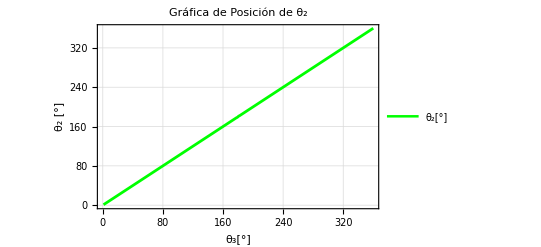

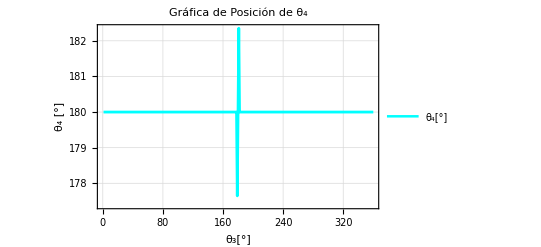

```mathematica
tabla1 = Table[{i,(θ2/.SolPos[i])/Degree},{i,1,360,1}];
tabla2 = Table[{i,(θ4/.SolPos[i])/Degree},{i,1,360,1}];

p1=ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ_3[°]","θ_2 [°]"},
PlotLabel->"Gráfica de Posición de θ_2",
PlotLegends->{"θ_2[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005]},
ImageSize->400]

p2=ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ_3[°]","θ_4 [°]"},
PlotLabel->"Gráfica de Posición de θ_4",
PlotLegends->{"θ_4[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Cyan,Thickness[0.005]},
ImageSize->400]
```

## Solución de Velocidad

```mathematica
Clear[θ2,θ3,θ4];
Clear[ω2,ω3,ω4];
Clear[α2,α3,α4];
```

```mathematica
RPM=(1/15)*60;
ω3=(2*Pi*RPM)/60  (*rad/s*)
(*ω3 = 1.5708; *)

For[i=1,i≤360,i+=1,

θ3=i*Degree;

SolVel[i]=Solve[{
vel1⟦1⟧==0,
vel1⟦2⟧==0}/.SolPos[i],
{ω2,ω4}]//Flatten;];(*Flatten saca los elementos de un conjunto*)

SolVel[90]
SolVel[180]
SolVel[270]
SolVel[360]
```

(2 π)/15

{ω2→0.00731045,ω4→2.7921}

{ω2→378827.,ω4→2.52552×10^6}

{ω2→-0.00731045,ω4→2.7921}

{ω2→-197373.,ω4→1.31582×10^6}

## Gráficas de Velocidad

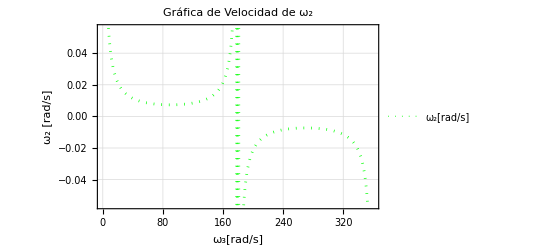

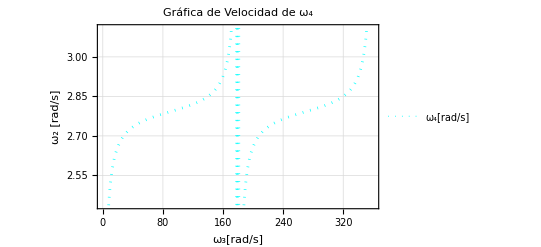

```mathematica
tabla3 = Table[{i,(ω2/.SolVel[i])},{i,1,360,1}];
tabla4 = Table[{i,(ω4/.SolVel[i])},{i,1,360,1}];

v1=ListPlot[tabla3,
Frame->True,
FrameLabel->{"ω_3[rad/s]","ω_2 [rad/s]"},
PlotLabel->"Gráfica de Velocidad de ω_2",
PlotLegends->{"ω_2[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005],Dotted},
ImageSize->400]

v2=ListPlot[tabla4,
Frame->True,
FrameLabel->{"ω_3[rad/s]","ω_2 [rad/s]"},
PlotLabel->"Gráfica de Velocidad de ω_4",
PlotLegends->{"ω_4[rad/s]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Cyan,Thickness[0.005],Dotted},
ImageSize->400]
```

## Solución de Aceleración

```mathematica
Clear[θ2,θ3,θ4];
Clear[ω2,ω3,ω4];
Clear[α2,α3,α4];

RPM=(1/15)*60;
ω3=(2*Pi*RPM)/60;  (*rad/s*)
α3 = 0.000001; (*rad/s.b2*) 

For[i=1,i≤360,i+=1,

θ3=i*Degree;

SolAcel[i]=Solve[{
acel1⟦1⟧==0,
acel1⟦2⟧==0}/.SolPos[i]/.SolVel[i],
{α2,α4}]//Flatten;];(*Flatten saca los elementos de un conjunto*)
```

## Gráficas de Aceleración

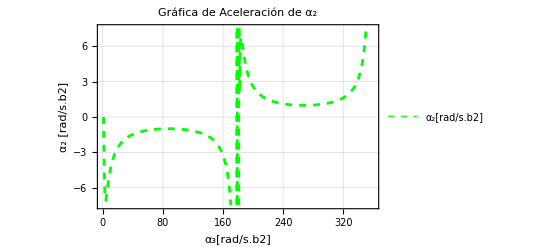

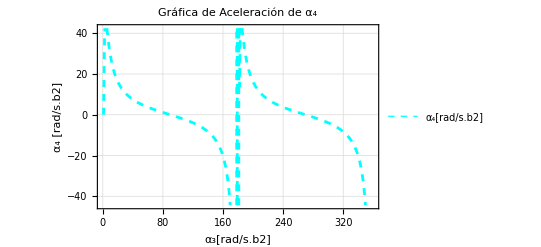

```mathematica
tabla5 = Table[{i,(α2/.SolAcel[i])},{i,1,360,1}];
tabla6 = Table[{i,(α4/.SolAcel[i])},{i,1,360,1}];

a1=ListPlot[tabla5,
Frame->True,
FrameLabel->{"α_3[rad/s.b2]","α_2 [rad/s.b2]"},
PlotLabel->"Gráfica de Aceleración de α_2",
PlotLegends->{"α_2[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Green,Thickness[0.005],Dashed},
ImageSize->400]
a2=ListPlot[tabla6,
Frame->True,
FrameLabel->{"α_3[rad/s.b2]","α_4 [rad/s.b2]"},
PlotLabel->"Gráfica de Aceleración de α_4",
PlotLegends->{"α_4[rad/s.b2]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{Cyan,Thickness[0.005],Dashed},
ImageSize->400]
```

## Gráficas en conjunto

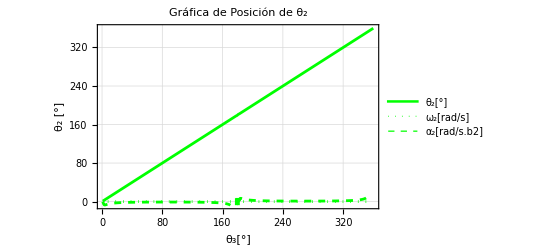

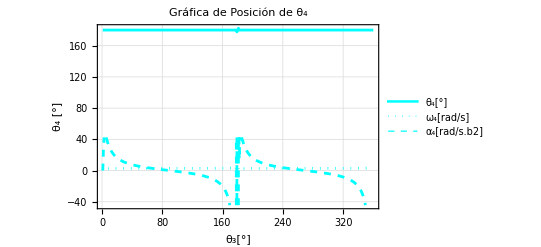

```mathematica
Show[p1,v1,a1,PlotRange->All]
Show[p2,v2,a2,PlotRange->All]
```

## Simulación

```mathematica
Clear[θ2,θ3,θ4];

Animate[

θ3=i*Degree;

x={1,0,0};
y={0,1,0};
k={0,0,1};
cero={0,0,0};

(*-----DEFINIENDO GEOMETRICAMENTE-----*)

eslabon1=Cylinder[{cero,0.03*k},0.05];(*Tierra*)
eslabon1a=Cylinder[{{-.025,0,0},{-.025,0,0.07}},0.01];(*Eje*)
eslabon2a=Cylinder[{cero,R3},0.01]/.SolPos[i];(*Barra Derecha*)
eslabon2b=Cylinder[{R1+0.05*k,R1+R2+0.05*k},0.01]/.SolPos[i];(*Barra izquierda*)
eslabon2c=Cylinder[{R3,R3+R4},0.011]/.SolPos[i];(*Barra soporte*)
ejea=Cylinder[{R3-0.011*k,R3+0.011*k},0.010];
ejeB=Cylinder[{R1+R2-0.011*k,R1+R2+0.07*k},0.010]/.SolPos[i];
(*-----PRIMA-----*)
eslabon2pa=Cylinder[{cero,R3p},0.01]/.SolPos[i];(*Barra Derecha*)
eslabon2pb=Cylinder[{R1+0.05*k,R1+R2p+0.05*k},0.01]/.SolPos[i];(*Barra izquierda*)
eslabon2pc=Cylinder[{R3p,R3p+R5},0.011]/.SolPos[i];(*Barra soporte*)
ejeC=Cylinder[{R3p-0.011*k,R3p+0.011*k},0.010];
ejeD=Cylinder[{R1+R2p-0.011*k,R1+R2p+0.07*k},0.010]/.SolPos[i];
(*-----BIPRIMA-----*)
eslabon2bpa=Cylinder[{cero,R3bp},0.01]/.SolPos[i];(*Barra Derecha*)
eslabon2bpb=Cylinder[{R1+0.05*k,R1+R2bp+0.05*k},0.01]/.SolPos[i];(*Barra izquierda*)
eslabon2bpc=Cylinder[{R3bp,R3bp+R6},0.011]/.SolPos[i];(*Barra soporte*)
ejeE=Cylinder[{R3bp-0.011*k,R3bp+0.011*k},0.010];
ejeF=Cylinder[{R1+R2bp-0.011*k,R1+R2bp+0.07*k},0.010]/.SolPos[i];

(*-----DEFINIENDO CARACTERISTICAS-----*)
tierra=Graphics3D[{Black,eslabon1}];
eje=Graphics3D[{Yellow,eslabon1a}];
barra2a=Graphics3D[{Red,eslabon2a}];
barra2b=Graphics3D[{Red,eslabon2b}];
barra2c=Graphics3D[{Green,eslabon2c}];
pernoa=Graphics3D[{Black,ejea}];
pernoB=Graphics3D[{Black,ejeB}];
(*-----PRIMAS-----*)
barra2pa=Graphics3D[{Red,eslabon2pa}];
barra2pb=Graphics3D[{Red,eslabon2pb}];
barra2pc=Graphics3D[{Green,eslabon2pc}];
pernoC=Graphics3D[{Black,ejeC}];
pernoD=Graphics3D[{Black,ejeD}];
(*-----BIPRIMAS-----*)
barra2bpa=Graphics3D[{Red,eslabon2bpa}];
barra2bpb=Graphics3D[{Red,eslabon2bpb}];
barra2bpc=Graphics3D[{Green,eslabon2bpc}];
pernoE=Graphics3D[{Black,ejeE}];
pernoF=Graphics3D[{Black,ejeF}];


Show[tierra,eje,barra2a,barra2b,barra2c,barra2pa,barra2pb,barra2pc,
barra2bpa,barra2bpb,barra2bpc,pernoa,pernoB,pernoC,pernoD,pernoE,pernoF,
Axes->True,
AspectRatio->1,
AxesLabel->{"X [in]","Y [in]","Z [in]"},
ImageSize->400,
ViewVertical->{0,1,0},
ViewPoint->{0,0,Infinity},
PlotRange->{{-0.3,0.3},{-0.3,0.3},{-1,1.3}}
],{i,1,360,1},AnimationRunning->False]
```